```mathematica
Lecture 6:Modules, Recursion
```

## Modules and local variables

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
Clear[n,k];
n=1;
Module[{k=4},n=n+k; k=n]
n
k
```

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
f[L_List]:=Module[{A=L/.{x_/;Positive[x]->1,x_/;Negative[x]->-1}},
And[FreeQ[A,{___,1,1,___}],FreeQ[A,{___,-1,-1,___}]]]
```

## Recursions

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
f[n_Integer/;n>=0]:=If[n<=1,1,n f[n-1]]
f/@Range@10
```

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
Clear[f]
f[n_]:=If[n<=1,1,f[n-1]+f[n-2]]
f/@Range@10
```

{1,2,3,5,8,13,21,34,55,89}

### Exercise Subsection

Recall from Exercise Set 4 that a Gray code (see https://en.wikipedia.org/wiki/Gray_code ) is an ordering of all bit strings (which are lists with elements either 0 or 1) such that consecutive bit strings differ in exactly one position.  Using the idea outlined in Set 4, we can recursively define a gray code; see this example:

```mathematica
GrayCode[n_]:=If[n==1,{{0},{1}},Join[Prepend[#,0]&/@GrayCode[n-1],
Prepend[#,1]&/@Reverse@GrayCode[n-1]]]
```

### Exercise Subsection

The Euclidean algorithm finds the greatest common divisor of a and b recursively.  Write down the values iteratively taken by a and b in the recursion below when starting with a=13 and b=21.

```mathematica
Euclidean[a_,b_]:=If[b==0,a,Euclidean[b,Mod[a,b]]]
```

### Exercise Subsection

Define a recursive function named MergeLists[L1_,L2_,L3_:{}] that takes in three lists L1, L2, and L3 (as an optional argument that defaults to {}) of nondecreasing numbers and outputs the sorted list with the numbers found in L1 an L2. The function should do the following:

1. Find the smaller of the two first elements in L1 and L2, say s.
2. Remove s from L1 (or L2) and append s to L3.
2. Repeat until both L1 and L2 are empty, then return L3.

You may not use any built-in sorting operations to do this exercise.

```mathematica
MergeLists[L1_List,L2_List,L3_:{}]:=
If[L1=={}||L2=={},Join[L3,L1,L2],
If[First@L1<=First@L2,
MergeLists[Rest@L1,L2,Append[L3,First@L1]],
MergeLists[L1,Rest@L2,Append[L3,First@L2]]]]
```

### Exercise Subsection

Merge sort (see https://en.wikipedia.org/wiki/Merge_sort ) is is a divide and conquer algorithm for sorting a list of numbers.  It works on the list L by 

1. Returning L in the case when L contains only one element, 
2. Merging (using the MergeLists function defined in the previous exercise) the list L[[;;1]] of length 1 containing only the first element on L and the Mergesort -ed list L[[2;;]].

Create a recursive function called Mergesort[L_List] that takes a list L as an input and returns the list in nondecreasing order.  You may not use any built-in sorting operations.

```mathematica
Mergesort[L_List]:=If[Length@L<=1,L,MergeLists[L[[;;1]],Mergesort@L[[2;;]]]]
```

## Memoization

### Exercise Subsection

The Pell numbers are defined by P_0=0, P_1= 1 and P_n= 2 P_(n-1)+P_(n-2) for n ≥ 2.  Write a recursive function Pell that returns P_n and then verify that

P_n= ((1 + √2)^n- (1 - √2)^n)/(2 √2)

holds for 0 ≤n ≤ 100.  The function Pell should take advantage of memoization.

### Exercise Subsection

The Catalan sequence (see https://en.wikipedia.org/wiki/Catalan_number ) is defined such that c[0] = 1 and c[n+1] is equal to the sum 

c[0] c[n] + c[1] c[n-1] + ... + c[n] c[0]

Using Timing to find the 15th Catalan number c[15] without using memoization and then compare Timing to find c[15] when implementing memoization.

### Exercise Subsection

The Yellowstone sequence is the sequence y[n] with y[1] = 1, y[2] = 2, y[3] = 3, and then y[n] is the smallest number not already on the list such that the greatest common divisor (the GCD) of y[n] and y[n-1] is 1 and the greatest common divisor of y[n] and y[n-2] is not 1.   Define this sequence recursively, taking advantage of memoization.   Then Map y to the first 100  positive integers.

```mathematica
y[n_]:=y[n]=If[n<=3,n,Module[{k=1},
While[Or[
GCD[k,y[n-1]]!=1,
GCD[k,y[n-2]]==1,
MemberQ[y/@Range[n-1],k]],
k+=1];
k]]
y/@Range@100
```

{1,2,3,4,9,8,15,14,5,6,25,12,35,16,7,10,21,20,27,22,39,11,13,33,26,45,28,51,32,17,18,85,24,55,34,65,36,91,30,49,38,63,19,42,95,44,57,40,69,50,23,48,115,52,75,46,81,56,87,62,29,31,58,93,64,99,68,77,54,119,60,133,66,161,72,175,74,105,37,70,111,76,117,80,123,86,41,43,82,129,88,135,92,125,78,145,84,155,94,165}

### Exercise Subsection

Using memoization, define a sequence a[n] such that a[1]=1 and otherwise a[n+1] is equal to a[n]/n if this is an integer and n a[n] otherwise. What is a[100]?

```mathematica
Clear[a]
```

```mathematica
a[n_]:=a[n]=If[n==1,1,If[Divisible[a[n-1],(n-1)],a[n-1]/(n-1),(n-1)a[n-1]]]
a[100]
```

8355422572174063769250070528925600

### Exercise Subsection

Suppose f[n] is a function such that f[1]=1 and f[2 n] = f[n] and f[2n+1] = f[2n] + 1 for all positive integers n.  Find the first value of n for which f[n] = 10.

### Exercise Subsection

The Hénon map, see (https://en.wikipedia.org/wiki/H%C3%A9non_map ) is a pair of sequences x[n] and y[n] defined by x[0]=1, y[0]=1, x[n]=1-1.4 x[n-1]^2 + y[n-1] , and y[n] = 0.3 x[n-1].

Find the list of pairs {x[n],y[n]} for n = 0, 1,...,10000, and then use the command ListPlot on this set of pairs to visualize them in the plane.

```mathematica
Clear[x,y]
x[n_]:=x[n]=If[n==0,1,1-1.4 x[n-1]^2 + y[n-1]]
y[n_]:=y[n]=If[n==0,1,.3 x[n-1]]
```

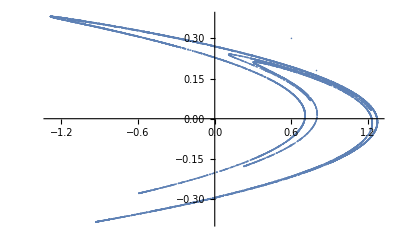

```mathematica
ListPlot[{x@#,y@#}&/@Range@10000]
```